```mathematica
(*慣性モーメントの計算*)
ClearAll["Global`*"];
(*integrate{r^2 dmass}*)
(*ρ*integrate{r^2 dv}*)
(*integrate{r^2 dmass}*)

distanceFromAxis[X_,O_,axis_]:=X-O-Dot[X-O,Normalize[axis]]*Normalize[axis];

MOI[axis_]:=FullSimplify@Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]
MOI[{1,0,0}]
MOI[{0,1,0}]
MOI[{0,0,1}]
```

1/12 Lx Ly Lz (Ly^2+Lz^2)

1/12 Lx Ly Lz (Lx^2+Lz^2)

1/12 Lx Ly (Lx^2+Ly^2) Lz

```mathematica
rhoALM=(2.70(*g/cm^3*))/1000/0.01^3;
Lx=5/100;(*m*)
Ly=29/100(*m*)
Lz=10/100;(*m*)
d=0.004058086021437735;
MOI[axis_]:=rhoALM*FullSimplify[
Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]
-Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}]
]
MOI[{1,0,0}]
MOI[{0,1,0}]
MOI[{0,0,1}]
```

29/100

0.00924492

0.00158923

0.00843057

```mathematica
ClearAll["Global`*"];
(*d=0.0045;(*板厚*)*)
Lx=0.05;(*m*)
Ly=0.29;(*m*)
Lz=0.1;(*m*)
Vol=Lx*Ly*Lz;(*m^3*)
s=0.68;(*kg/kg*)
rho=1000(*kg/m^3*);
(*mass in the experiment*)
massExp=Vol*s*rho;
Print["the volume of the floating body : ",Vol, "m^3"]
Print["mass of the floating body : ",massExp, "kg"]
```

the volume of the floating body : 0.00145m^3

mass of the floating body : 0.986kg

```mathematica
(*一般的なアルミの重さ*)
rhoALM=(2.70(*g/cm^3*))/1000/0.01^3;
volume[d_]:=Integrate[1,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]-Integrate[1,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}]
ans=Solve[rhoALM*volume[d]==massExp&&d<Lx/2&&d<Ly/2&&d<Lz/2,d]
d=d/.ans[[1]]
Iy=NIntegrate[rhoALM*Sqrt[x^2+z^2],{x,-Lx/2,Lx/2},{z,-Lz/2,Lz/2}]-NIntegrate[rhoALM*Sqrt[x^2+z^2],{x,-Lx/2+d,Lx/2-d},{z,-Lz/2+d,Lz/2-d}]


Print["the volume of the floating body : ",volume[d], "m^3"]
Print["mass of the floating body : ",rhoALM*volume[d], "kg"]
Print["Iy = ",Iy]
```

{{d→0.00405809}}

0.00405809

0.123274

the volume of the floating body : 0.000365185m^3

mass of the floating body : 0.986kg

Iy = 0.123274

```mathematica
Clear["Global`*"]
pitchEXP=Import[NotebookDirectory[]<>"../SPHERIC_TestCase12/Rotation.dat"][[1;;]];
pitchEXP[[1]]
pitchEXP=pitchEXP[[2;;]];
motionsEXP=Import[NotebookDirectory[]<>"../SPHERIC_TestCase12/Motions.dat"][[1;;]];
motionsEXP[[1]]
heaveEXP={#1,#2}&@@@motionsEXP[[2;;,{1,2}]];
surgeEXP=motionsEXP[[2;;,{3,4}]];
```

{Time,(s),Roll,(degrees)}

{Time,(s),Heave,(m),Time,(s),Sway,(m)}

```mathematica
name="~/BEM/Hadzic2005/result.json";
imported=ImportString[StringReplace[Import[name,"text"],{"NaN"->"null","nan"->"null"}],"JSON"];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported][[;;]];
titles=imported[[;;,1]];
Column[titles,Background->{{LightRed,Pink}},Frame->True]
```

cpu_time
float_COM
float_EK
float_EP
float_accel
float_area
float_force
float_pitch
float_roll
float_torque
float_velocity
float_yaw
simulation_time
wall_clock_time
water_E
water_EK
water_EP
water_volume

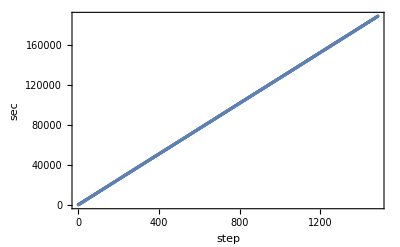

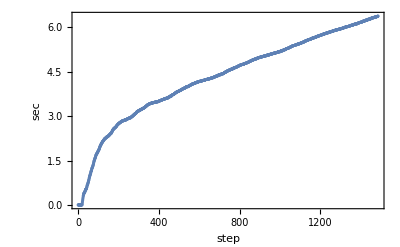

```mathematica
ListPlot[getData["cpu_time"]
,Frame->True
,FrameLabel->{"step","sec"}
]
ListPlot[getData["simulation_time"]
,Frame->True
,FrameLabel->{"step","sec"}
]
```

```mathematica
ListPlot[Transpose[{getData["simulation_time"],getData["float_force"]}]]
```

-Graphics-

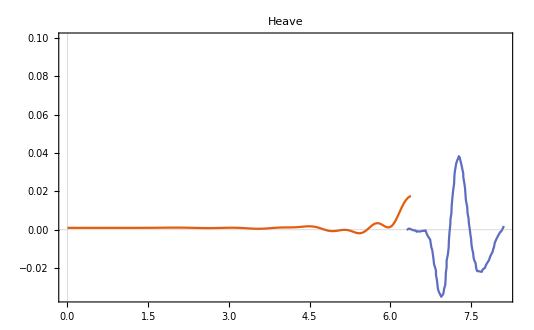

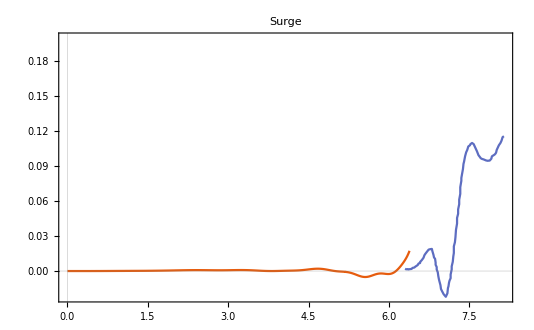

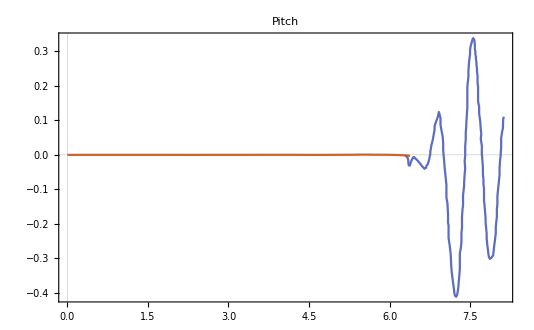

```mathematica
ListPlot[{Transpose[{getData["simulation_time"],getData["float_COM",3]-0.39}],{#1,#2}&@@@heaveEXP},PlotLabel->"Heave",PlotRange->{All,0.1},Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{getData["simulation_time"],getData["float_COM",1]-2.11}],{#1,#2}&@@@surgeEXP},PlotLabel->"Surge",PlotRange->{All,0.2},PlotRange->All,Joined->True,PlotTheme->"Scientific"]
ListPlot[{Transpose[{getData["simulation_time"],-getData["float_pitch"]}],{#1,#2/180*Pi}&@@@pitchEXP},PlotLabel->"Pitch",PlotRange->All,Joined->True,PlotTheme->"Scientific"]
```

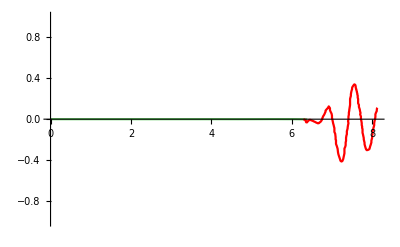

```mathematica
ListPlot[
{Transpose[{getData["simulation_time"],-getData["float_pitch"]}],
{#1,#2/180*Pi}&@@@pitchEXP},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{True,True,True},
PlotRange->{Automatic,{-1,1}}
(*PlotRange->{{0,2.25},{-1.,1.}},*)
(*PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,Italic],Style["H/H_0",FontSize->20,Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotTheme->"Scientific",
ImageSize->500,
PlotLegends->Placed[LineLegend[{"Measured Data","Simulated Data"},LegendMarkerSize->20,LabelStyle->20],{0.75,0.15}]*)
]
```